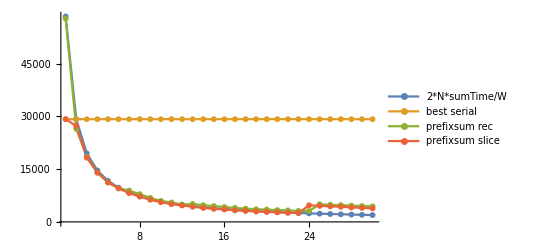

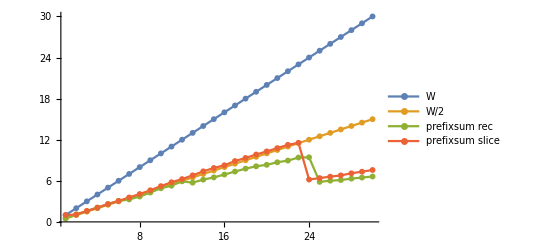

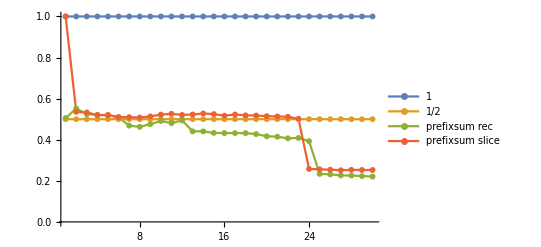

0.551893

0.406966

0.535617

0.51168

```mathematica
nameRec := "prefixsum rec"
nameSlice := "prefixsum slice" 
timesRec := {57752.85,26439.67,18535.97,14005.30,11240.53,9545.35,8896.53,7885.69,6814.70,5941.34,5520.47,4922.21,5091.65,4730.68,4489.68,4219.50,3970.94,3752.74,3593.37,3500.06,3351.61,3259.57,3104.30,3094.33,4993.73,4851.11,4773.68,4619.28,4509.80,4404.91}
timesSlice := {29183.76,27243.11,18265.83,14031.72,11214.71,9535.05,8177.05,7181.66,6315.77,5589.91,5041.52,4670.10,4293.42,3951.46,3706.99,3528.72,3283.97,3125.61,2965.82,2835.01,2708.42,2592.51,2528.06,4721.08,4562.45,4416.92,4297.63,4112.52,3981.62,3850.03}
best1 := 29183.76

idealTime[w_] := 2*best1/w
idealTimes := Map[idealTime, Range[30]]
ListLinePlot[{idealTimes, ConstantArray[best1, 30], timesRec, timesSlice}, PlotRange -> All, PlotMarkers ->{{●, 6}, {●, 6}, {●, 6}, {●, 6}}, PlotLegends -> {"2*N*sumTime/W", "best serial", nameRec, nameSlice}]

speedupFunc[x_] := best1/ x
speedupRec := Map[speedupFunc, timesRec]
speedupSlice := Map[speedupFunc, timesSlice]
ListLinePlot[{Range[30], Range[0.5, 15, 0.5], speedupRec, speedupSlice}, PlotRange -> All, PlotMarkers ->{{●, 6}, {●, 6}, {●, 6}, {●, 6}}, PlotLegends -> {"W", "W/2", nameRec, nameSlice}]

efficFuncRec[x_] := speedupRec[[x]]/ x
efficFuncSlice[x_] := speedupSlice[[x]]/ x
efficRec := Map[efficFuncRec, Range[30]]
efficSlice := Map[efficFuncSlice, Range[30]]
ListLinePlot[{ConstantArray[1, 30], ConstantArray[0.5, 30], efficRec, efficSlice}, PlotRange -> All, PlotMarkers ->{{●, 6}, {●, 6}, {●, 6}, {●, 6}}, PlotLegends -> {"1", "1/2", nameRec, nameSlice}]

Print[efficRec[[2]]]
Print[efficRec[[22]]]
Print[efficSlice[[2]]]
Print[efficSlice[[22]]]
```